# Physics 230 -- Lab 3 (Plotting Lists and Functions)

## Fall 2015 - Transtrum Labs developed by John S. Colton, BYU Physics & Astronomy, based in part on past labs by Branton Cambell and Steve Turley

The ability to visualize functions and data is often a prerequisite to really understanding them, especially when dealing with multi-dimensional problems.  The powerful graphical-visualization capabilities of Mathematica will enhance your ability to explore complicated functions and datasets and to present what you discover to others.

```mathematica
Clear["`*" ]
```

## Setting Plot Options

### Plot options

You’ve already learned a bit about making plots. There are a wide variety of options that you can use to change the way your plot looks. Here’s an example for a plot you might make for damped harmonic motion.

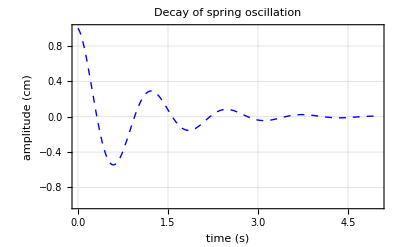

```mathematica
Plot[Cos[5 t] E^-t,{t,0, 5}, PlotRange->{-1,1}, PlotStyle-> {Blue, Thick, Dashed},  GridLines->Automatic,GridLinesStyle->Directive[Red,Dotted], PlotLabel->"Decay of spring oscillation", Frame->True,FrameLabel -> {"time (s)","amplitude (cm)"},LabelStyle->{Purple,Bold},AxesOrigin->{0,-1}]
```

Play around with the various plot settings for a minute or two until you get a sense for what they do. Please use F1 on the options if you need some help to decipher them. Also look at the help page for for Plot and the Options for Graphics tutorial to get warmed up.

Multiple functions. Multiple functions can be plotted together by giving Mathematica a list of functions as the first argument for Plot. Also, when you are plotting multiple functions the “PlotStyle” option needs to become a list of lists instead of a sinlge PlotStyle list. The first list refers to the first function, the second list to the second function, and so forth. Here’s an example, with a few more plot options. Again, you should play around with the given options for a bit to see what they do.

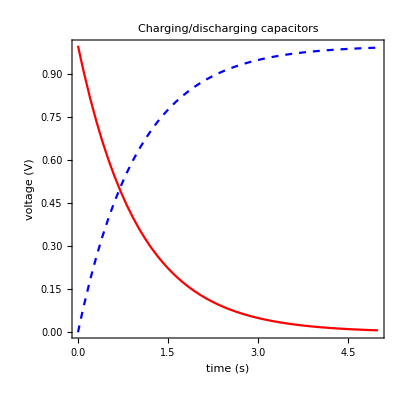

```mathematica
Plot[{1-E^-t,  E^-t},{t,0, 5}, PlotStyle-> {{Blue, Dashed},{Red}}, Frame->True, PlotLabel->Style["Charging/discharging capacitors",FontColor->Gray,FontSlant->Italic,FontWeight->Bold, FontSize->15,FontFamily->"Ariel"],FrameLabel->{Style["time (s)",FontFamily->"Ariel"], Style["voltage (V)", FontFamily->"Ariel"]} , ImageSize->400 , AspectRatio->1]
```

#### Assignment 1. Sin, Cos, and Tan graphs with options

Make a plot of sinx, cosx, and tanx functions from -2π to 2π with a single Plot command. Make the three functions have different colors. Make one solid, one dashed, and one dotted. Use Exclusions→{-3Pi/2,-Pi/2,Pi/2,3Pi/2} as an option for the tangent function so that it doesn’t plot a line through the graph as tangent crosses over from +∞ to -∞. Give the plot a title, along with x- and y-axes labels. Pick an appropriate ImageSize and AspectRatio. Include GridLines if you feel like it.

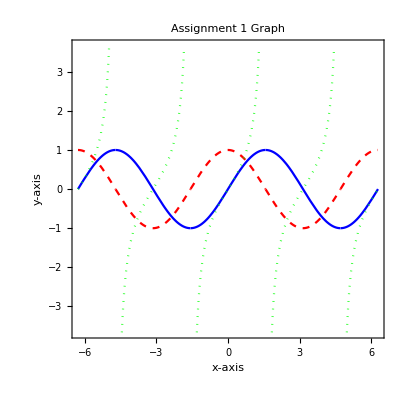

```mathematica
Plot[{Sin[x],Cos[x],Tan[x]},{x,-2Pi,2Pi},PlotStyle-> {{Blue},{Red,Dashed},{Green,Dotted}},Exclusions->{-3Pi/2,-Pi/2,Pi/2,3Pi/2},PlotLabel->"Assignment 1 Graph",Frame->True,FrameLabel->{"x-axis","y-axis"},ImageSize->400 , AspectRatio->1, GridLines->{{-2Pi,-Pi,Pi,2Pi},{-3,-2,-1,1,2,3}}]
```

### Improving plots via “sampling”

While the functions that you plot often seem to be smooth curves, Mathematica really plots a finite number of connected line segments. These line segments connect points where the function has been evaluated. This is called “sampling” the function, and poor sampling can lead to imperfections in the plots. 

To see an example of sampling errors, evaluate the plot below where sin(1/x) progresses towards infinitely fine oscillations as x approaches 0.  The x-axis is plotted in log scale. Drag a corner of the plot to enlarge it. Notice how many of the oscillations in the left-hand part of the graph fail to go completely up to 1 and completely down to -1. That’s incorrect--the sin function should always oscillate between -1 and +1.

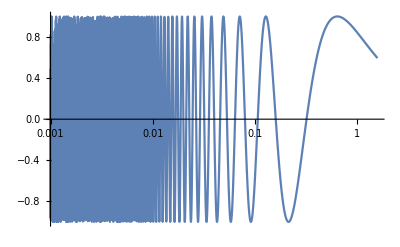

```mathematica
LogLinearPlot[Sin[1/x],{x,0.001,Pi/2},PlotRange->All]
```

This type of error can be corrected via two special plot options, PlotPoints and MaxRecursion, which govern how Mathematica samples the function. PlotPoints establishes a set of n evenly-spaced points at which to evaluate the function, and MaxRecursion further increases the number of points by adding additional points in the regions where they are needed most, that is in regions where the function has sharp features. Each recursion doubles the number of points. For example, if we start with 10 points, and perform 2 recursions, the overall total number of points plotted will be 40. Evaluate the example below for a new function... the Mesh→All option reveals the sampled points.

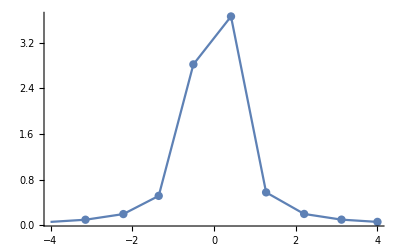

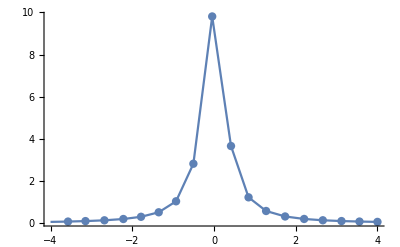

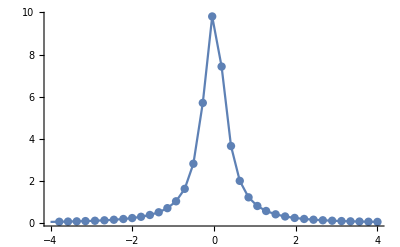

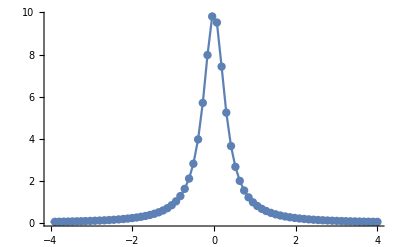

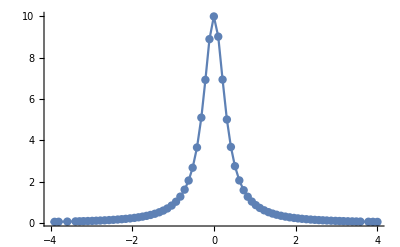

```mathematica
fsampling[x_] := 1/(x^2+0.1)
Plot[fsampling[x],{x,-4,4},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->0]
Plot[fsampling[x],{x,-4,4},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->1]
Plot[fsampling[x],{x,-4,4},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->2]
Plot[fsampling[x],{x,-4,4},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->10,MaxRecursion->3] (* this plots 80 pts *)
Plot[fsampling[x],{x,-4,4},PlotRange->All,Mesh->All,PlotStyle->PointSize[0.015],PlotPoints->40,MaxRecursion->1]  (* this also plots 80 pts *)
```

The default settings for PlotPoints (50) and MaxRecursion (Automatic) are often adequate, but you can easily increase them if the sharp features of your plots don’t look right.

#### Assignment 2. Improve the sin(1/x) plot

Use PlotPoints and/or MaxRecursion to improve the LogLinearPlot of sin(1/x) from above, so that the oscillations near the origin clearly extend from -1 to 1.

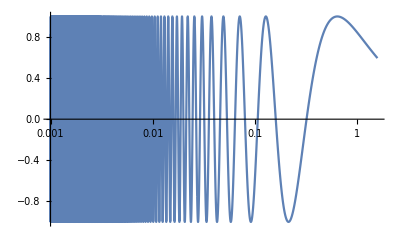

```mathematica
LogLinearPlot[Sin[1/x],{x,0.001,Pi/2},PlotRange->All,PlotPoints->1000,MaxRecursion->Automatic]
```

## Different Types Of Plots

### Log scale plots

Log-scale plots are very important analytical tools; among other things they can help you decide on what kind of dependence your data has, for example exponential, logarithmic, or power law. However, Mathematica doesn’t allow you to easily change from one to another. Instead of having a log-scale axis being one of the options for Plot (which would make a lot of sense), you must specify log-scale axes by changing the function you use to create the plot: LogPlot, LogLinearPlot, or LogLogPlot.

#### Assignment 3. A few log scale plots

(a) Use LogPlot, LogLinearPlot and LogLogPlot to graph e^x over the range from x = 0.01 to 100.  Which log-scale scheme produced linear output and why? Be sure you can explain this.
(b) Repeat for ln(x). Hint: The natural log function in Mathematica is not called “Ln”.
(c) Repeat for x^3.

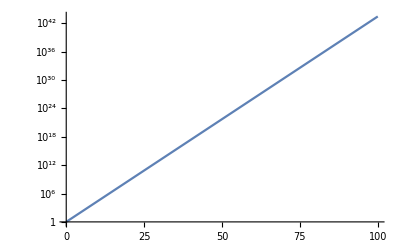

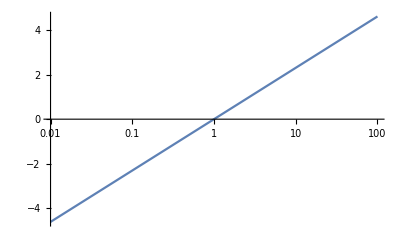

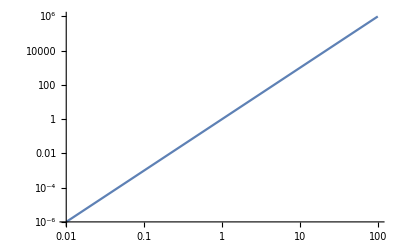

```mathematica
LogPlot[E^x,{x,.01,100}]
LogLinearPlot[Log[x],{x,.01,100}]
LogLogPlot[x^3,{x,.01,100}]
```

### Plot 3D

Plot3D is a simple way to make a 3D plot of a function of two variables. (The function value itself is the third dimension.) It uses many of the same options as Plot, but has many of its own options. Notice how you can rotate the viewing angle by clicking and dragging on the image.

```mathematica
Plot3D[Sinc[x]^2 Sinc[2 y]^2,{x,-9,9},{y,-9,9},PlotRange->All]  (* Incidentally, this is the diffraction pattern for a rectangular slit. And in case you've forgotten or haven't learned yet, sinc(x) = sin(x)/x *)
```

-Graphics3D-

#### Assignment 4. A Plot3D example

Use Plot3D to graph (x^2+y^2+0.1)^-1 over a sufficiently wide range of x and y to properly illustrate the central peak.  Apply PlotRange to prevent the top of the peak from getting clipped off.  Hide the Mesh and employ a ColorFunction to change the appearance with a different color gradient. (See the guide page on Color Schemes for a list of many of the built-in color gradients.) Use BoxRatios (analogous to AspectRatio in 2D graphics) to make the bounding box be cubic (i.e. BoxRatios → {1,1,1}).  Use Boxed (analogous to Frame in 2D graphics) to hide the bounding box, and also hide the Axes.  Apply FaceGrids → All to further customize the plot.

```mathematica
Plot3D[1/(x^2+y^2+.1),{x,-1,1},{y,-1,1},PlotRange->All,BoxRatios->{1,1,1},Mesh->None,ColorFunction->"DarkTerrain",Boxed->False,Axes->False,FaceGrids->All]
```

-Graphics3D-

### Contour plots

ContourPlot and DensityPlot (really just a specific type of contour plot with a large number of undrawn contour lines) are additional tools that allow you to visualize functions of two variables.

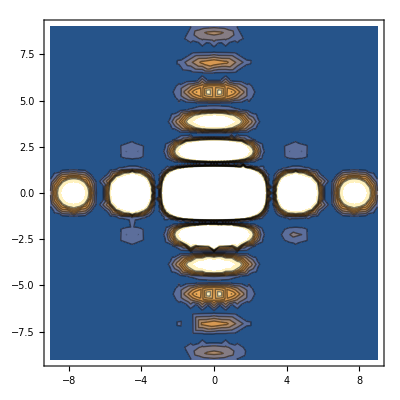

```mathematica
ContourPlot[Sinc[x]^2 Sinc[2 y]^2,{x,-9,9},{y,-9,9}]
```

Things to notice: Strange jagged edges in any plot are usually a give-away that you need to increase the resolution through PlotPoints and/or MaxRecursion. In this case, I’ll increase the number of PlotPoints to 50 to fix the problem. (While 50 pts is the default number of PlotPoints in regular graphs done with Plot, the default is much less for more advanced graphs. That’s to save time in plotting. For this ContourPlot, the default seems to be 15.)

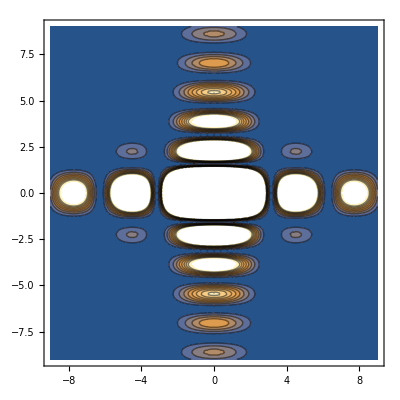

```mathematica
ContourPlot[Sinc[x]^2 Sinc[2 y]^2,{x,-9,9},{y,-9,9}, PlotPoints->50]
```

Things to observe: Try adding a Contours option to the plot (setting to a number). And try turning the ContourLines off (setting to False).

Here’s a very similar thing with DensityPlot. The similarities ought to be apparent.

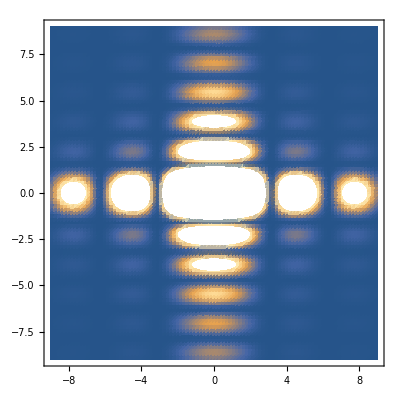

```mathematica
DensityPlot[Sinc[x]^2 Sinc[2 y]^2,{x,-9,9},{y,-9,9},PlotPoints->100]
```

4D plots? To make a plot of a function of three variables, in principle you would need four spatial dimensions (the three variables, plus the function value itself). But just as a contour plot can transform a “Plot3D” into a series of 1D curves plotted on a 2D surface, ContourPlot3D can transform the hypothetical 4D plot into a series of 2D surfaces plotted in 3D space. We won’t do anything with it, but it’s good to know it’s there. Look at the help file to see some capabilities.

#### Assignment 5. Visualizing 3D space as contours

Use both ContourPlot and Plot3D to visualize the two-variable expression cos(π x) + cos(π y) over a range that extends from -2 to 2 along both axes.  Compare and contrast the two methods of plotting the function, and be able to explain to the TA how the one is a contour visualization of the other.

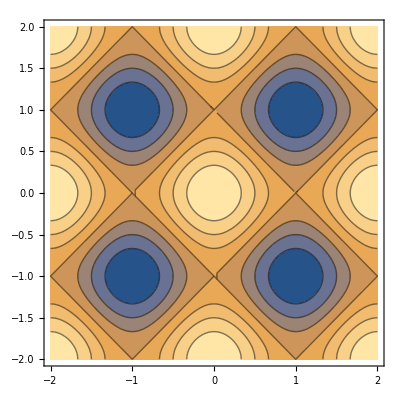

-Graphics3D-

```mathematica
ContourPlot[Cos[Pi*x]+Cos[Pi*y],{x,-2,2},{y,-2,2}]
Plot3D[Cos[Pi*x]+Cos[Pi*y],{x,-2,2},{y,-2,2}]
```

### Contours to visualize solutions of equations

Instead of letting ContourPlot select its own contours, you can select the specific contour that gets plotted. Here’s the sinc^2(x) sinc^2(y) function again:

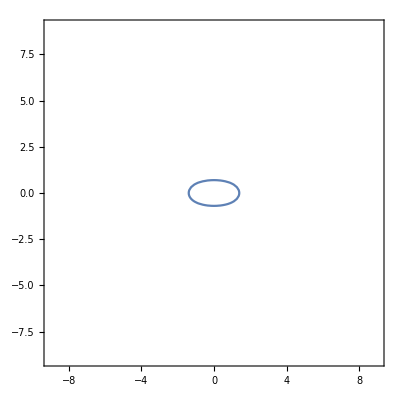

```mathematica
ContourPlot[Sinc[x]^2 Sinc[2 y]^2==0.5,{x,-9,9},{y,-9,9}]  (* Note the double equals sign! This is a contour near the top of the central peak. *)
```

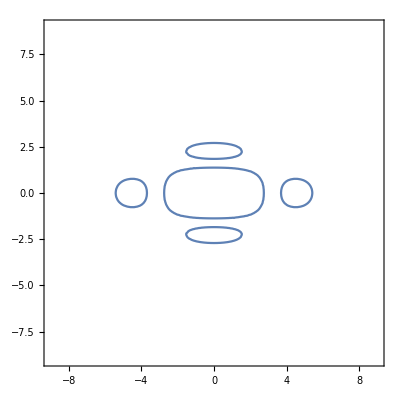

```mathematica
ContourPlot[Sinc[x]^2 Sinc[2 y]^2==0.02,{x,-9,9},{y,-9,9},PlotPoints->50] (* This uses a smaller value of the function. It is a contour that is lower down. *)
```

Things to notice: The curve plotted on the top graph tells you everywhere that the function is equal to 0.5...basically just an oval around the main peak. Look back at the Plot3D plot of this function to convince yourself that that makes sense. The bottom graph is more interesting, because there are more spots that the function can have a value of 0.02.

Conic sections. This trick can also be used to, for example, plot 2D conic sections. Here’s an ellipse for you:

1/9 (-1+x)^2+1/25 (-2+y)^2

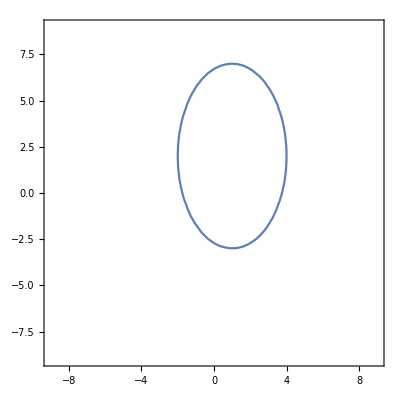

```mathematica
ellipseLHS=((x-x0)/a)^2 + ((y-y0)/b)^2    /.{x0->1, y0->2, a-> 3,b-> 5}
ContourPlot[ellipseLHS==1,{x,-9,9},{y,-9,9}]
```

#### Assignment 6. Solutions to complicated simultaneous equations

Determine approximate (x,y) coordinates of the eight solutions to these two simultaneous equations:  cos(πx)+cos(πy)=0.5  and  x^2+y^2=2.  Do this graphically by sending a list of the two equations to ContourPlot (so the contours of both equations get plotted on the same graph); the intersection of the two sets of contours will reveal the points that are solutions to both. Use ContourStyle to make the two sets of contours appear with colors different than the default.

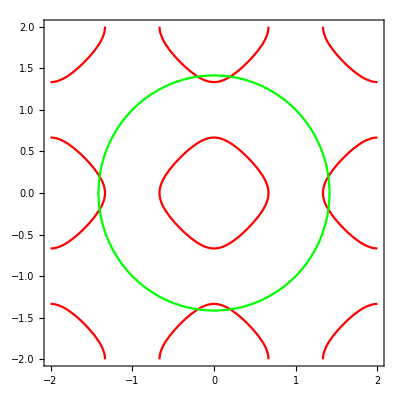

```mathematica
ContourPlot[{Cos[Pi*x]+Cos[Pi*y]==.5,x^2+y^2==2},{x,-2,2},{y,-2,2},PlotRange->All,ContourStyle->{Red,Green}]
```

### Vector field plots

The functions that we’ve plotted so far have been scalar functions, ones which return a simple number as a function of x, y, and/or z. However, many functions in physics are vector functions, ones which return a vector as a function of x, y, and/or z. Scalar/vector functions are often termed scalar/vector fields. Examples of such vector functions are electric and magnetic fields, or even something as simple as a function that describes air currents in a room. These are vector functions because to fully describe wind currents (for example) you must specify both magnitude and direction of the air’s velocity at each point in the room. Each position in space (x,y,z) will therefore have a particular vector associated with it. Vectors are represented by arrows, where the magitude of the vector is conveyed by the length of the arrow.

For the moment let’s consider only two dimensions. Let’s visualize the electric field produced at an arbitrary point (x,y) from a point charge q located at the origin: E(x,y)=1/(4 πϵ_0)q/r^2 r̂.  

To explain that equation: first, the point where you want to know the field, (x,y), is called the vector r, i.e. r=(x,y). The distance from the origin to that point is the magnitude of r and is given by the Pythgorean Theorem,  i.e.  r=(x^2+y^2)^0.5.  The unit vector r̂ describes the direction of the field at that point. It points away from the origin. That is, it’s a unit vector in the same direction as r. Since a unit vector is a vector divided by its magnitude, r̂=r/r and the term in the equation, (r̂)/r^2, can be written as r/r^3.  Putting all of that together, and with q and 4 πϵ_0 each set equal to 1 for simplicity, the electric field equation becomes:  E(x,y) = (x,y)/((x^2+y^2)^1.5),  or  E(x,y) = (x/((x^2+y^2)^1.5),y/((x^2+y^2)^1.5)).  (Make sure you understand where the exponent of 1.5 in the denominator comes from.) 

This function is now in the form that can be visualized with VectorPlot (if a function of x and y) or VectorPlot3D (if a function of x, y, and z). The first parameter of the function needs to be a list containing the components of the field function, E_x and E_y in this case. Here’s what it looks like:

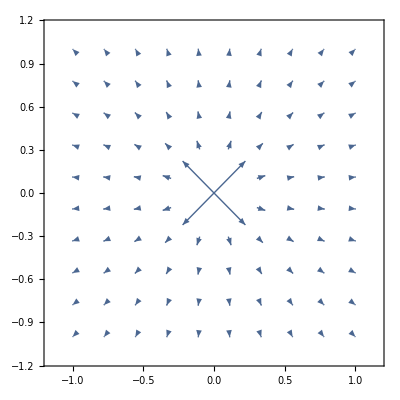

```mathematica
VectorPlot[{x/(x^2+y^2)^1.5,y/(x^2+y^2)^1.5},{x,-1,1},{y,-1,1},VectorPoints->10]  (* VectorPoints is a lot like PlotPoints *)
```

You can use StreamPlot to connect the arrows together. This loses the magnitude information and generates what are essentially the field lines.

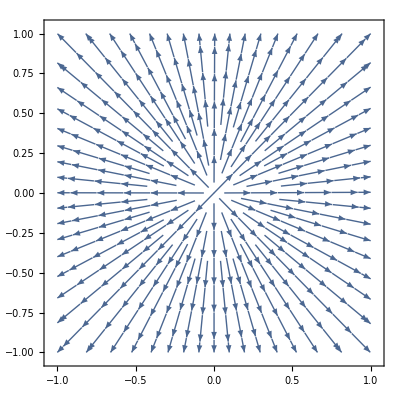

```mathematica
StreamPlot[{x/(x^2+y^2)^1.5,y/(x^2+y^2)^1.5},{x,-1,1},{y,-1,1}]  (* Notice that StreamPlot doesn't use the VectorPoints option *)
```

The extension into three dimensions is hopefully clear for VectorPlot3D. (Unfortunately there is no StreamPlot3D.) Notice how I’ve inserted the z’s into the next equation. Play around a bit with the viewing angle by clicking and dragging inside the box.

```mathematica
VectorPlot3D[{x/(x^2+y^2+z^2)^1.5,y/(x^2+y^2+z^2)^1.5,z/(x^2+y^2+z^2)^1.5},{x,-1,1},{y,-1,1},{z,-1,1}, VectorPoints->5]
```

-Graphics3D-

#### Assignment 7. Electric field from two point charges

A more interesting picture is the field from two point charges. To get a two-charge picture, there are two things you need to know in order to modify the equations appropriately. First, the charges will no longer be at the origin. Therefore, you need to know that the field at (x,y) from a charge located at the point (x0,y0) is just the same equation given above, but with x replaced by x-x0  and  y replaced by y-y0, everywhere in the equation. Second, the total field at (x,y) is the sum of the fields produced by each charge. With those in mind, do the following:

(a) Make a VectorPlot* and a StreamPlot** of the field from two like charges: one at x = 0.5 and one at x = -0.5. 
(b) Repeat, for two charges of opposite signs (a so-called "electric dipole"). To get the appropriate contribution from the negative charge, just use q = 1 in your starting equation.

* Hint: I found VectorPoints->10 to work well.
** Remember StreamPlot doesn’t use the VectorPoints option.

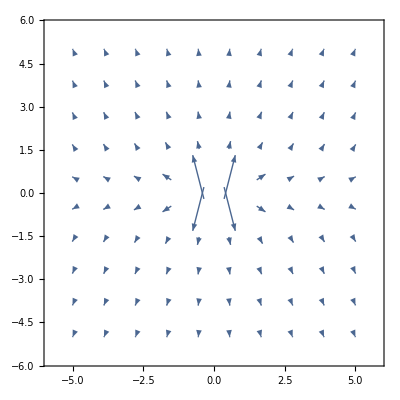

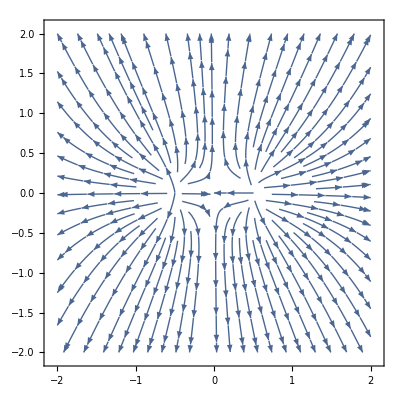

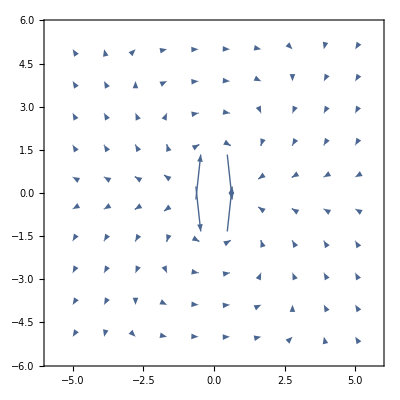

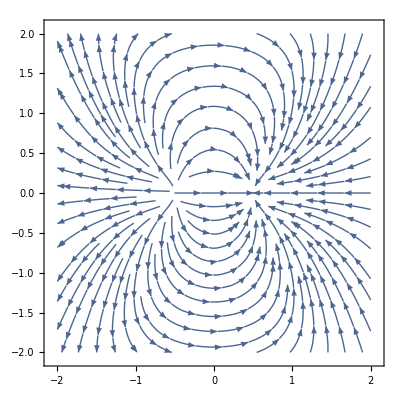

```mathematica
VectorPlot[{((x-.5)/((x-.5)^2+y^2)^1.5)+(x+.5)/((x+.5)^2+y^2)^1.5,(y/((x-.5)^2+((y)^2)^1.5))+(y)/((x+.5)^2+((y)^2)^1.5)},{x,-5,5},{y,-5,5},VectorPoints->10] 

StreamPlot[{((x-.5)/((x-.5)^2+y^2)^1.5)+(x+.5)/((x+.5)^2+y^2)^1.5,(y/((x-.5)^2+((y)^2)^1.5))+(y)/((x+.5)^2+((y)^2)^1.5)},{x,-2,2},{y,-2,2}] 
VectorPlot[{-((x-.5)/((x-.5)^2+y^2)^1.5)+(x+.5)/((x+.5)^2+y^2)^1.5,-(y/((x-.5)^2+((y)^2)^1.5))+(y)/((x+.5)^2+((y)^2)^1.5)},{x,-5,5},{y,-5,5},VectorPoints->10] 

StreamPlot[{-((x-.5)/((x-.5)^2+y^2)^1.5)+(x+.5)/((x+.5)^2+y^2)^1.5,-(y/((x-.5)^2+((y)^2)^1.5))+(y)/((x+.5)^2+((y)^2)^1.5)},{x,-2,2},{y,-2,2}]
```

### Parametric functions and plots

A “trajectory” is a 1D curve which might exist in a 2D plane or in 3D space. Even though the path of the trajectory may exist in 2 or 3 dimensions, the trajectory itself is considered to be 1D because it has only one degree of freedom, which is the position along the curve. In other words, the position along the curve can be described by a single variable. A natural choice of variable might be time, t. Speaking of the 2D case, if you know how x and y each vary with time, then you can figure out the shape of the trajectory of the object, y(x). The shape need not be a simple function y(x), though, because there could be multiple y values for a given x depending on the specific trajectory. A plot of the trajectory obtained by plotting (x(t), y(t)) for all possible values of t is called a parametric plot.

Consider the motion of a projectile in free-fall with some initial velocity v_0 at some initial angle θ: x(t)=x_0+v_0 cos(θ)t, and y(t)=y_0+v_0 sin(θ)t- 1/2 g t^2. Let’s make a ParametricPlot of the trajectory for a certain choice of initial conditions:

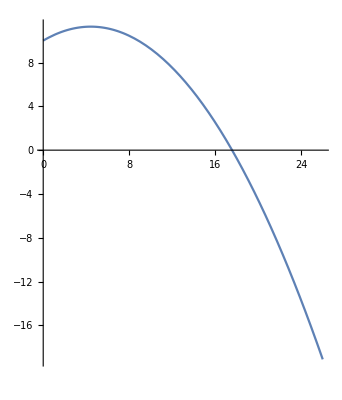

```mathematica
x0 = 0; y0 = 10; v0 = 10; θ=30 Degree; g = 9.8;
x[t_] = x0 + v0 Cos[θ] t;
y[t_] = y0 + v0 Sin[θ] t- 1/2 g t^2;
ParametricPlot[{x[t],y[t]},{t,0,3}]
```

Things to observe:  This is not a plot of anything vs time (although the y-position vs. t graph may look similar). This is a plot of the actual motion of the object plotted in real space--the axes are x and y, both in meters.

Here’s another example, to show you that a parametric plot doesn’t have to be a plot of a simple function. That is, the motion of the object could be such that there is more than one y-value for a particular x-value.

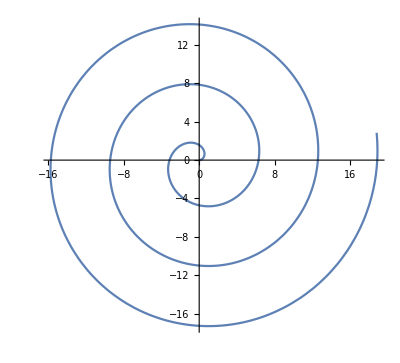

```mathematica
ParametricPlot[{t Cos[t], t Sin[t]},{t,0,19}]
```

Things to observe:  If you plot {Cos[t], Sin[t]}, instead of a helix you will get a simple circle (traced out repeatedly). Try it! Then try some other choices for x(t) and y(t) on your own. See what cool shapes you can make.

Additional Info: Mathematica’s plot functions PolarPlot, RevolutionPlot3D and SphericalPlot3D are variations on the parametric-plot theme.  They simplify the process of constructing a parametric plot in certain specific cases.  For example, a polar plot is useful when the parametric variable is the phase angle ϕ  (i.e. tan(ϕ) = y/x) and where the distance √(x^2+y^2)has an explicit dependence on ϕ. And ParametricPlot3D can be used as a natural extension of ParametricPlot to plot trajectories--or even surfaces--in 3-dimensional space.

#### Assignment 8. Plot of helix

A charged particle experiences a force from a magnetic field according to this equation:  F = qv×B, where q is the magnitude of the charge, v is the charge’s velocity, and B is the magnetic field at the location of the charge. This is sometimes called the Lorentz force. (We’ll assume for now that there is no electric field present.) Suppose the magnetic field is in the z-direction. If the particle is traveling in the z-direction, the cross product results in no force on the particle (because ẑ×ẑ=0). It is completely unaffected by the field. Conversely, if the particle is traveling only in the x-y plane, the cross product means that the force will always be perpendicular to the velocity. That causes circular motion, just like a ball on a string being spun in a circle where the tension force is always perpendicular to the velocity of the ball. If the particle has a combination of all three components, there will be circular motion in the x-y plane superimposed with a constant velocity in the z-direction. That produces a helix. 

Make a 3D parametric plot of such a helix. The x-coordinate should be proportional to cos(ωt), the y-coordinate proportional to sin(ωt), and the z-coordinate just proportional to  t  itself. Be able to explain those three choices. Pick a suitable choice of ω to get a good looking plot. Some trial and error might be in order.

```mathematica
ω=2Pi;
ParametricPlot3D[{Cos[ω*t],Sin[ω*t],t},{t,0,Pi}]
```

-Graphics3D-

### Plotting lists

Since a previous lab already discussed how to plot data points via ListPlot, we’ll not spend much time on this today. Here’s the guide page on Data Visualization, though, where it contains information on all of the various types of list plots: ListPlot, ListPlot3D, ListPointPlot3D, ListContourPlot, ListContourPlot3D, and so forth.

#### Assignment 9. Using “Show” with different types of plots

(a) As mentioned in lab 1, Show can be used to merge two plots together. Use Show to combine a list plot of the following “listdata” with a regular Plot of the function y=x^2, with x going from 0 to 2. 
(b) Suppose plot1 is the plot of the data points and plot2 is the plot of the function. Figure out when there is a difference between Show[plot1,plot2] and Show[plot2,plot1]. Hint: try plotting y(x) with x going from 0 to 3.

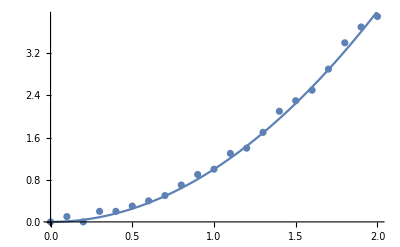

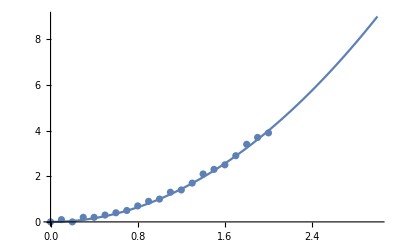

```mathematica
listdata={{0., 0.}, {0.1, 0.1}, {0.2, 0.}, {0.3, 0.2}, {0.4, 0.2}, {0.5, 0.3}, {0.6, 0.4}, {0.7, 0.5},  {0.8, 0.7}, {0.9, 0.9}, {1., 1.}, {1.1, 1.3}, {1.2, 1.4}, {1.3, 1.7}, {1.4, 2.1}, {1.5, 2.3},  {1.6, 2.5}, {1.7, 2.9}, {1.8, 3.4}, {1.9, 3.7}, {2., 3.9}};
Show[ListPlot[listdata],Plot[x^2,{x,0,2}]];
plot1=ListPlot[listdata];
plot2=Plot[x^2,{x,0,3}];
Show[plot1,plot2]
Show[plot2,plot1]
```

## Manipulating And Animating Graphs

### Manipulate/Animate

A nice extension of Mathematica’s plotting features is the ability to create a graph with adjustable parameters that you can change in real time. The syntax is fairly straightforward: you take an existing plot, change one or more of the fixed parameters into a variable, then wrap the whole thing inside a Manipulate command (which also specifies the range over which the now adjustable parameter or parameters can be varied).

Damped harmonic oscillator, revisited. As an example, let’s adjust the damped harmonic oscillator plot from the top of this lab. The first graph here is the same as it was above; the second graph has an adjustable oscillating frequency and damping period.

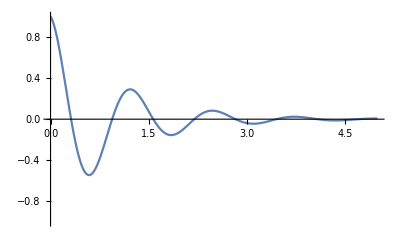

```mathematica
Plot[Cos[5 t] E^-t,{t,0, 5},PlotRange->{-1,1}]
```

```mathematica
Manipulate[Plot[Cos[w t] E^(-t/tau),{t,0, 5},PlotRange->{-1,1}], {w,0,10},{tau,0.001,10}]
```

Things to observe: Play around with the Manipulate controls to see what happens to a damped harmonic oscillator as you change the oscillating frequency and/or damping time.

Automatic animation. The Animate command is essentially identical, but allows Mathematica to automatically manipulate the parameters for you. Here’s an example, with some of the most useful options added in for good measure. You can have it change both parameters at the same time, or one at a time.

```mathematica
Animate[Plot[Cos[w t] E^(-t/tau),{t,0, 5},PlotRange->{-1,1}], {w,0,10},{tau,0.001,10}, AnimationRate->3,AnimationDirection->ForwardBackward,AnimationRunning->True]
```

Things to observe: The Background option for Plot is probably not one that you have experimented with yet Try taking out  Background→White  to see why I’ve included it. That flashing that occurs is because of the default background color of this StyleSheet; if you create animations on a fresh, unformatted notebook you won’t have that issue. (Depending on your version of Mathematica the flashing may not be an issue even in this StyleSheet. If it’s not an issue for you, please disregard.)

There’s a lot more information in the tutorial/guide pages: Introduction to Manipulate, Dynamic Visualization and Interactive Manipulation. And there are some other related commands, such as ListAnimate. You don’t need to look at those all right now, but you can refer to them in the future as needed.

#### Assignment 10. Combining cosine waves.

When you add two sinusoidal waves together that have different amplitudes and phases but the same frequency, the result will always be a sinusoidal wave with the same frequency, but with yet another amplitude and phase. Those of you who took Phys 123 from me should even know how to calculate the amplitude and phase of the resulting function using complex numbers. For this assignment we'll determine the amplitude and phase of the sum through trial and error in a manipulatable graph.

(a) Define a function, y_1(t) = A_1 cos(5t + ϕ_1), where the amplitude A_1 and phase ϕ_1 are each given by  RandomReal[{0.1, 4}]  commands. Do the same for a second function, y_2. Plot them both together from 0 to 2π, and observe that their periods are each 2π/5. 

(b) Add the two functions together to obtain y_3(t):  y3[t_] = y1[t] + y2[t].  Plot it and notice that y_3(t)  also has a period of 2π/5. 

(c) Now, plot y3(t) on the same graph as a fourth function, Acos(5 t+ ϕ), where A and ϕ are parameters you can manipulate. Have A going from 0 to 8 and ϕ going from 0 to 2π. Plot y3 and this manipulatable function for times between 0 and 2π. Adjust your parameters manually until the two curves match up, and then read off the final values of the parameters by clicking on the + signs by the sliders.

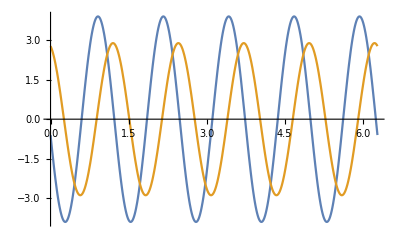

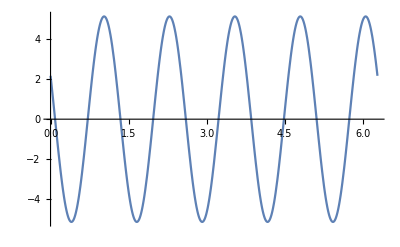

```mathematica
y1[t_]=RandomReal[{.1,4}]*Cos[5t+RandomReal[{.1,4}]];
y2[t_]=RandomReal[{.1,4}]*Cos[5t+RandomReal[{.1,4}]];
Plot[{y1[t],y2[t]},{t,0,2Pi}]
y3[t_]=y1[t]+y2[t];
Plot[y3[t],{t,0,2Pi}]
Animate[Plot[{y3[t],A*Cos[5t+ϕ]},{t,0,2Pi},PlotRange->2Pi],{A,0,8},{ϕ,0,2Pi},AnimationDirection->ForwardBackward,AnimationRunning->True];
Manipulate[Plot[{y3[t],A*Cos[5t+ϕ]},{t,0,2Pi},PlotRange->2Pi],{A,0,8},{ϕ,0,2Pi}]
```

## Behind The Curtain: Graphics Objects

When you create a plot, Mathematica actually assembles a collection of Graphics objects for you. There may be times that you would like to define your own Graphics objects by hand--for example, I have had many students use Graphics objects to make cool things happen in their term projects. Here are a couple of simple examples for you to get started, in case that’s something that you would like to do:

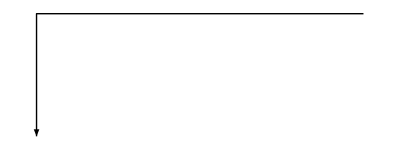

```mathematica
Graphics[Arrow[{{4,3/2},{0,3/2},{0,0}}]]    (* Press F1 on Arrow to see what the parameters do. Or experiment on your own. *)
```

You specify options by including them in a list before the object:

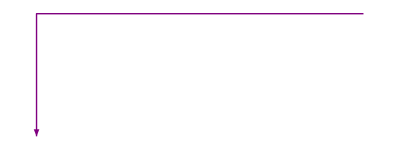

```mathematica
Graphics[{Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}]}]
```

Many of the same options that are available to Plot are available to Graphics.

```mathematica
objects[x_] := Circle[{x,0},x/2]
Manipulate[ Graphics[objects[x] ,Axes->True,PlotRange->{{0,30},{-15,15}},AspectRatio->1, Background->White],{x,0,20}]
```

You include multiple graphics objects together by merging them together in a list, with the options for each item just prior to the item itself.

```mathematica
twoobjects[x_] :={{Purple,Arrowheads[Large],Arrow[{{30,10},{x,10},{x,0}}]}, 
 Dashed, Circle[{x,0},x/2]}
Manipulate[ Graphics[twoobjects[x] ,Axes->True,PlotRange->{{0,30},{-15,15}},AspectRatio->1,Background->White],{x,0,20}]
```

#### Assignment 11. A square inscribed in a circle

Use Graphics objects to inscribe a blue square inside a solid red disk.The disc should have radius 1 and be centered at the origin. Show the axes with an  Axes→True  option in your Graphics command. Hints: (1) The graphics objects you will need are called Rectangle and Disk. Create a few individual rectangles & disks to get a feel for those commands before trying to put them together. (2) The positions of the square’s corners will be related to the disk’s radius through the square root of 2:  the upper right corner = (cos45°, sin45°), for example.

1/(√2)

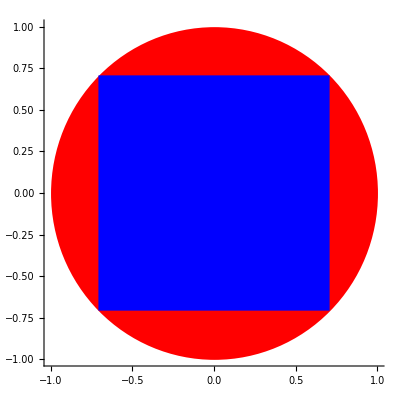

```mathematica
A=Sqrt[2]/2
Graphics[{Red,Disk[{0,0},1],Blue,Rectangle[{-A,-A},{A,A}]},Axes->True]
```

## Additional Assignments

#### Assignment 12. Combining traveling waves

A traveling plane wave has the form ACos[kx - ωt], where A is the amplitude of the wave, k is the "wave number" = 2π/wavelength (how many radians of oscillation there are each meter for a frozen instant in time), and ω is the angular frequency = 2π/period (how many radians of oscillation there are each second at a fixed location in space). The speed of the wave  v = wavelength × frequency = (2π/k) × (ω/2π) = ω/k. 

Define a traveling wave function with A = 1 (in some units), k = 4 rad/m and ω = 2 rad/s. 
(a) Animate the plot in time (0 to 10 s) over the spatial region from 0 to 10 m. (Be sure to use the  Background→White  option for all your animations if you do your work in this notebook.) 
(b) Simultaneously animate a left moving wave, ACos[kx + ωt]. 
(c) Animate the sum of the two waves. Fix the y-axis scale using the PlotRange option so that it doesn’t continuously rescale on you. What is this? 
(d) Animate the sum of two right going waves, but change one to have k = 5 rad/m and ω = 2.5 rad/s  (note that ω/k, the wave's velocity, is the same for both). What is this?

```mathematica
Animate[Plot[{Cos[4j-2t],Cos[4j+2t]},{j,0,10},PlotRange->{-3,3}],{t,0,10},AnimationRate->3,AnimationDirection->Forward,AnimationRunning->True]
Animate[Plot[Cos[4j-2t]+Cos[4j+2t],{j,0,10},PlotRange->{-3,3}],{t,0,10},AnimationRate->3,AnimationDirection->Forward,AnimationRunning->True]
Animate[Plot[Cos[4j-2t]+Cos[5j-2.5t],{j,0,10},PlotRange->{-3,3}],{t,0,10},AnimationRate->3,AnimationDirection->Forward,AnimationRunning->True]
```

#### Assignment 13, Extra Credit. Magnetic field from a wire

Magnetic fields are produced by currents of charges. The magnetic field produced at position (x,y) by a current flowing in a very long, straight wire on the z-axis is given by this equation: B=((μ_0 I)/(2π))(-y x̂  +  x ŷ)/(x^2+y^2). Here I is the current (in amps) and μ_0 is a fundamental constant... but for our purposes you can set the stuff inside the parentheses equal to 1. Use VectorPlot3D to visualize this field over the range from -1 to +1 in all three directions. Hint: use the unit vectors in the equation to break B into B_x, B_y, and B_z components (B_z=0).

```mathematica
VectorPlot3D[(y/(x^2+y^2))+(x/(x^2+y^2)),{x,-1,1},{y,-1,1}]
```

VectorPlot3D::argrx: VectorPlot3D called with 3 arguments; 4 arguments are expected.

```mathematica
VectorPlot3D[{-y/(x^2+y^2),x/(x^2+y^2),0},{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

## Wrap-up

The following functions were discussed in today's lab, or are very closely related:
Regular plots: Plot, LogPlot, LogLogPlot, LogLinearPlot
Contour plots: ContourPlot, DensityPlot, ContourPlot3D 
Vector plots: VectorPlot, StreamPlot, VectorPlot3D
Parametric plots: ParametricPlot, ParametricPlot3D, PolarPlot, RevolutionPlot3D, SphericalPlot3D
List plots: ListPlot, ListPlot3D, ListPointPlot3D, ListContourPlot, ListContourPlot3D
Combining plots: Show
Interactive/Animated plots: Manipulate, Animate, ListAnimate
Graphics objects: Arrow, Circle, Disk, Rectangle

Potentially useful summary/tutorial pages:
Guide: Function Visualization
Tutorial: Options for Graphics
Guide: Data Visualization
Tutorial: Introduction to Manipulate
Guide: Dynamic Visualization
Guide: Interactive Manipulation